# Load data set from Data Drop and split to training set and test set

```mathematica
dataSet = Values[Databin["mLZ2ImvC"]];
```

```mathematica
shuffleDataSet = RandomSample[dataSet];
	TraningSet = shuffleDataSet[[;;140]];
	TestSet=shuffleDataSet[[141;;]];
	Short[TrainingSetRule = MapThread[Rule, {TraningSet[[All, 1]], TraningSet[[All, 2]]}],3]
	Short[TestSetRule = MapThread[Rule, {TestSet[[All, 1]], TestSet[[All, 2]]}],3]
```

{-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Left,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Right,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Left,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Right,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Right,-Graphics-→Forward,-Graphics-→Forward,«87»,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Right,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward}

{-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Left,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,«126»,-Graphics-→Forward,-Graphics-→Right,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Left,-Graphics-→Forward,-Graphics-→Left,-Graphics-→Right,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Right,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Right,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward,-Graphics-→Forward}

#### Find a classifier using da training set

```mathematica
classifier = Classify [TrainingSetRule , Method->"NeuralNetwork"]
```

ClassifierFunction[…]

#### Test the performance of the classifier using the test set

```mathematica
ClassifierMeasurements[classifier, TestSetRule, "Accuracy"]
```

0.882682

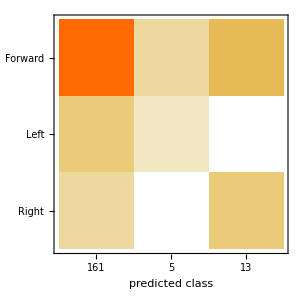

```mathematica
f = ClassifierMeasurements[classifier, TestSetRule, "ConfusionMatrixPlot"]
```